{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myblue}{RGB}{62, 85, 190},\definecolor{myred}{RGB}{195, 66, 50},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588},\AtBeginDocument{\color{white}}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

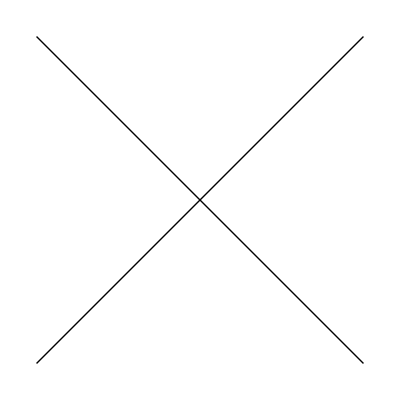
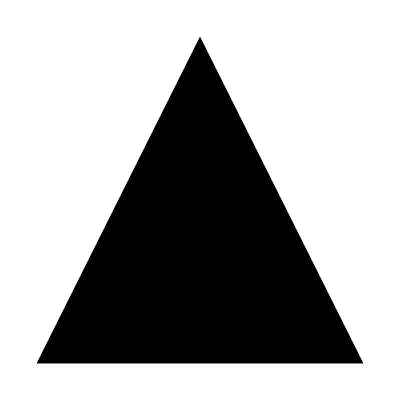

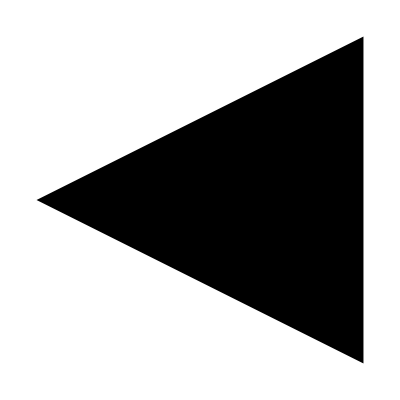
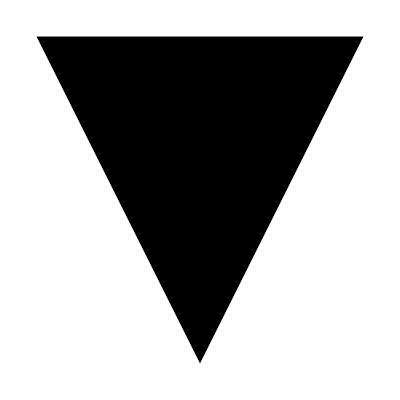
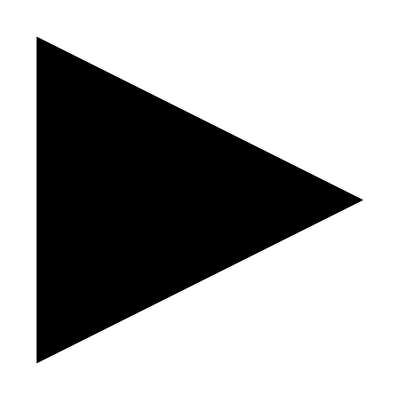
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<<MaTeX`
(*myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];*)

myblue=RGBColor[62/255,85/255,190/255];
myred=RGBColor[195/255,66/255,50/255];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.01;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;

SetOptions[MaTeX,FontSize->fontSize,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myblue}{RGB}{62, 85, 190}","\\definecolor{myred}{RGB}{195, 66, 50}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}",
"\\AtBeginDocument{\\color{white}}"}]
SetOptions[MatrixPlot,FrameTicksStyle->Black,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],ImageSize->imagSize,AspectRatio->1];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,FrameStyle->Black,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True,PlotMarkers->{halfTr[[2;;-1;;3]],Table[0.1,{i,4}]}ᵀ];
SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}},Joined->True];
SetOptions[ListDensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black,
PlotStyle->{{Thickness[thickness],myyellow},{Thickness[thickness],myblue},{Thickness[thickness],myred},{Thickness[thickness],mygreen}}];
SetOptions[DensityPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,ImageSize->imagSize,GridLines->Automatic,AspectRatio->1,FrameTicksStyle->Black];
align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .0;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{Black,Opacity[0], Thickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align],
   Graphics[{EdgeForm[{Black,Opacity[0], Thickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align],
   Graphics[{EdgeForm[{Black,Opacity[0], Thickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi,3π/2}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientWhiteRed","",{}},{"Gradients"},1,{0,1},{White,myred},""};
ColorData["GoogleGradientWhiteRed"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientWhiteBlue","",{}},{"Gradients"},1,{0,1},{myblue,White},""};
ColorData["GoogleGradientWhiteBlue"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
```

```mathematica
Clear[nL,diagonalize,eval,evec]
diagonalize[t_,m_,g_,χ_,nL_,k_]:=Module[{H,eval,evec,kk,order},
H=ConstantArray[0,{nL,nL}];
Do[
H[[i,i]]=t*Cos[k-χ*(2i-(nL+1))];
(*H[[i,i]]=t*Cos[k-χ*i];*)
,{i,1,nL}
];
(*H[[1,1]]=t*Cos[k-χ];
H[[2,2]]=t*Cos[k+χ];*)
Do[
H[[i,i+1]]=(m-g*Cos[k]);
H[[i+1,i]]=(m-g*Cos[k]);
,{i,1,nL-1}
];
{eval,evec}=Eigensystem[N[H]];
order=Ordering[eval];
eval=eval[[order]];
evec=evec[[order]];
evec=Table[Normalize[ev],{ev,evec}];
evec=evecᵀ;
{eval,evec}
(*Show[Table[Plot[eval[[i]]/.{k->kk*π},{kk,-1,1},ColorFunction->Function[{x,y},ColorData["GoogleGradient"][(evec[[i,1]]/.{k->(x-.5)*2π})^2]]],{i,1,nL}],PlotRange->2*{-1,1}]*)
]
```

```mathematica
Clear[nL]
mm=0.1;
gg=0.;
chi=0.025π;
(*chi=0.1π;*)
weights={};
plots={};
Monitor[
Do[
myblack=Black;
colors=Table[Directive[{Blend[{White,Black},i],Thickness[0.01]}],{i,0,1-1/nL,1/nL}];
solved=Table[diagonalize[-1.0,N[mm],N[gg],N[chi],nL,k*π],{k,-.99,.99,.001}];
ek0=diagonalize[-1.0,N[mm],N[gg],N[chi],nL,0][[1]];
(*If[nL<7,eF=ek0[[1]]+(ek0[[2]]-ek0[[1]])/2;];*)
eF=ek0[[1]]+(ek0[[2]]-ek0[[1]])/2;
order=Ordering[solved[[All,1,1]]];
ig=Flatten[Position[solved[[All,1,1]],n_ /; n<eF]];
(*ig=solved[[order,1,1]];*)
ig1=ig[[1]];
igN=ig[[-1]];
AppendTo[plots,ListPlot[solved[[All,1]]ᵀ,GridLines->{{},{eF}},GridLinesStyle->{Opacity[1],myred},Joined->True,DataRange->{-1,1},PlotMarkers->False,PlotStyle->colors,PlotRangePadding->{0.,0.1}]];
AppendTo[weights,Abs[solved[[igN,2,1,1]]/solved[[ig1,2,1,1]]]^2]
,{nL,2,(*Floor[π/chi]-1*)19}]
,nL]
```

```mathematica
ts=0.02*{1,1/GoldenRatio};
```

```mathematica
Floor[π/chi]-1
```

39

```mathematica
ticks={{{{0.0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1.0,MaTeX[""],ts},{1.,Rotate[MaTeX["\\epsilon/t"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1,MaTeX[""],ts}},{{0.85,MaTeX["k/\\pi"],.0}}],{None}}};
Manipulate[cwplot=Show[plots[[i]],FrameTicks->ticks,ImagePadding->{{20,2},{20,1}},ImageSize->8.6cm/2,PlotRange->1.2*{-1.,1.},PlotRangePadding->None],{i,1,Length[plots],1}]
```

```mathematica
ths=Thickness[.003];
ts=0.02*{1,1/GoldenRatio};
bs=20;
ticks={{{{10^-8,MaTeX[""],ts},{10^-16,MaTeX[""],ts},{10^-32,MaTeX["10^{-32}"],ts},{10^-64,MaTeX["10^{-64}"],ts},{10^-10,Rotate[MaTeX["\\left|\\frac{u_N}{u_1}\\right|^2"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{2,MaTeX["2"],ts},{10.0,MaTeX["10"],ts},{20,MaTeX["20"],ts},{30,MaTeX["30"],ts}},{{37.,MaTeX["N"],.0}}],{None}}};
wplot=ListLogPlot[weights,Joined->True,PlotRange->{10^-80,10},PlotStyle->Black,GridLines->None,FrameTicks->ticks,ImagePadding->(ip={{34,2},{20,2}}),ImageSize->8.6cm/2,Epilog->Inset[MaTeX["\\rm (c)"],{Length[weights]/2,-13.25}]]
```

-Graphics-

```mathematica
weights//Dimensions
```

{38}

```mathematica
ticks={{{{0.0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1.0,MaTeX[""],ts},{1.,Rotate[MaTeX["\\epsilon/t"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1,MaTeX[""],ts}},{{0.85,MaTeX["k/\\pi"],.0}}],{None}}};
cwplot1=Show[plots[[1]],FrameTicks->ticks,FrameStyle->White,ImagePadding->ip,ImageSize->8.6cm/2,PlotRange->1.2*{-1.,1.},PlotRangePadding->None,Epilog->Inset[MaTeX["\\rm (a)"],{0,1}]]
```

-Graphics-

```mathematica
ticks={{{{0.0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1.0,MaTeX[""],ts},{0.95,Rotate[MaTeX["\\epsilon_i(k)"],π/2],ts*0}},Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[{{0,MaTeX["0"],ts},{-1.0,MaTeX["-1"],ts},{1,MaTeX[""],ts}},{{0.85,MaTeX["k/\\pi"],.0}}],{None}}};
cwplot2=Show[plots[[-1]],FrameTicks->ticks,FrameTicksStyle->White,FrameStyle->White,PlotStyle->Thickness[.001],ImagePadding->ip,ImageSize->8.6cm/2,PlotRange->1.2*{-1.,1.},PlotRangePadding->None,Epilog->Inset[MaTeX[""],{0,1}]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Dropbox/Michele-Matteo-Andreas/mathematica

```mathematica
Export["uN_div_u1"<>".png",wplot,ImageResolution->400]
Export["cw_example1"<>".png",cwplot1,ImageResolution->400]
Export["cw_example2"<>".png",cwplot2,ImageResolution->400]
```

uN_div_u1.png

cw_example1.png

cw_example2.png